```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize-> 14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx[Ml_,Mnl_,m_,scale_]:={Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],scale{.016,0}}&/@(10^Range[-100,100,Ml]),
{Log10@#,"",scale{.016,0}}&/@(10^Range[-100,100,Mnl]),{Log10@#,"",scale{.008,0}}&/@Flatten[(10^Range[-100,100,1])*#&/@Range[1,9,m]]],Join[{Log10@#,"",scale{.016,0}}&/@(10^Range[-100,100,Mnl]),{Log10@#,"",scale{.008,0}}&/@Flatten[(10^Range[-100,100,1])*#&/@Range[1,9,m]]]};
Msunt = ToString[Subscript[Style["M",Italic],"⊙"],FormatType->StandardForm];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Constraints for monochromatic PBH mass functions

```mathematica
(* 0912.5297 *)
BBN = Import["BBN.dat"];
(* 2002.00898 *)
CMB = Import["CMB.dat"];
(* 0912.5297 *)
EGR = Import["EGR.dat"];
(* 1807.03075 *)
Voyager = Import["Voyager.dat"];
(* 1910.01285 *)
SUB = Import["SUB.dat"];
(* 1307.5798 *)
Kepler = Import["Kepler.dat"];
(* 0011506 *)
MACHO = Import["MACHO.dat"];
(* 0607207 *)
EROS = Import["EROS.dat"];
(* 2403.02386 *)
OGLE = Import["OGLE.dat"];
(* 1605.03665 *)
Eridanus = Import["Eridanus.dat"];
(* 1704.01668 *)
Segue1 = Import["Segue1.dat"];
(* 1712.02240 *)
SNe = Import["SNe.dat"];
(* 1406.5169 *)
WB = Import["WB.dat"];
(* 1705.00791 *)
xray = Import["xray.dat"];
(* 2405.05732 *)
LIGO = Import["LIGO.dat"];
(* 2303.17601 *)
LIGOlens = Import["LIGOlens.dat"];
(* 1903.10509 *)
Lya = Import["Lya.dat"];
(* 2002.10771 *)
acc = Import["acc.dat"];
(*2008.08077*)
DF=Import["DynEff.dat"];
(*2008.08077*)
LSS=Import["LSS.dat"];
(*2508.04767*)
lyIso=Import["LyIso.dat"];
(*2508.08238*)
PlIso=Import["PlIso.dat"];
(*1901.07120*)
OGLEHint=Import["OGLEhint.dat"];
(*2211.00013*)
SNEHint=Import["SNeHint.dat"];
(*2410.06251*)
OGLEhc=Log10[Import["OGLEhc.dat"]];
```

```mathematica
interpolate[log10m_,list_]:=Piecewise[{{Interpolation[list,InterpolationOrder->1][log10m],First@First@list<log10m<First@Last@list}},100]
BBNf[log10m_] = interpolate[log10m,BBN];
CMBf[log10m_] = interpolate[log10m,CMB];
EGRf[log10m_] = interpolate[log10m,EGR];
Voyagerf[log10m_] = interpolate[log10m,Voyager];
SUBf[log10m_] = interpolate[log10m,SUB];
Keplerf[log10m_] = interpolate[log10m,Kepler];
MACHOf[log10m_] = interpolate[log10m,MACHO];
EROSf[log10m_] = interpolate[log10m,EROS];
OGLEf[log10m_] = interpolate[log10m,OGLE];
Eridanusf[log10m_] = interpolate[log10m,Eridanus];
Segue1f[log10m_] = interpolate[log10m,Segue1];
SNef[log10m_] = interpolate[log10m,SNe];
WBf[log10m_] = interpolate[log10m,WB];
xrayf[log10m_] = interpolate[log10m,xray];
LIGOf[log10m_] = interpolate[log10m,LIGO];
LIGOlensf[log10m_] = interpolate[log10m,LIGOlens];
Lyaf[log10m_] = interpolate[log10m,Lya];
accf[log10m_] = interpolate[log10m,acc];
DFf[log10m_] = interpolate[log10m,DF];
LSSf[log10m_] = interpolate[log10m,LSS];
LyIf[log10m_] = interpolate[log10m,lyIso];
PlIsof[log10m_] = interpolate[log10m,PlIso];
OGLEhcf[log10m_] = interpolate[log10m,OGLEhc];
```

```mathematica
Mevap = 2.55*^-19;
```

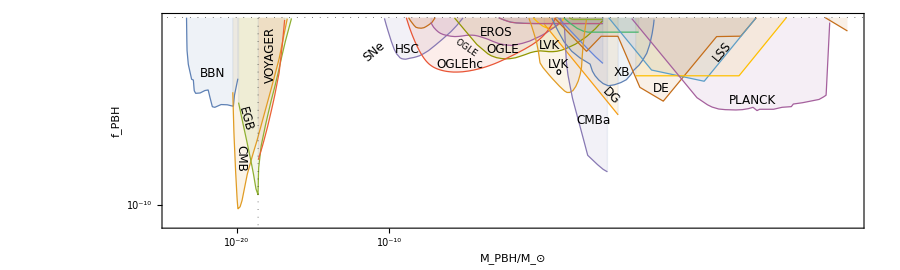

```mathematica
Show[Plot[{BBNf[x],CMBf[x],EGRf[x],Voyagerf[x],SUBf[x],Keplerf[x],SNef[x],MACHOf[x],EROSf[x],OGLEf[x],OGLEhcf[x],Eridanusf[x],Segue1f[x],SNef[x],WBf[x],xrayf[x],LIGOf[x],LIGOlensf[x],Lya[x],accf[x],DFf[x],LSSf[x],LyIf[x],PlIsof[x]},{x,-24,20},Filling->Top,PlotStyle->Thickness[0.001],FillingStyle->Opacity[0.1],PlotRange->{{-24,20.2},{-11,0}},PlotRangePadding->None,GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Black, Dotted],FrameLabel->{"M_PBH/"<>Msunt,"f_PBH"},AspectRatio->0.3,ImageSize->900,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{logticksx[2,1,1,0.4],logticksx[2,1,1,0.4]},ImagePadding->{{58,10},{42,10}}],
Graphics[Text[Rotate[Style["BBN",12],0Degree],{-21.6,-3.}]],
Graphics[Text[Rotate[Style["CMB",12],270Degree],{-19.7,-7.5}]],
Graphics[Text[Rotate[Style["EGB",12],285Degree],{-19.4,-5.4}]],
Graphics[Text[Rotate[Style["VOYAGER",12],90Degree],{-17.8,-2.}]],
Graphics[Text[Rotate[Style["HSC",12],0Degree],{-8.8,-1.7}]],
Graphics[Text[Rotate[Style["EROS",12],0Degree],{-3,-0.8}]],
Graphics[Text[Rotate[Style["OGLE",12],0Degree],{-2.6,-1.7}]],
Graphics[Text[Rotate[Style["OGLEhc",12],0Degree],{-5.4,-2.5}]],
Graphics[Text[Rotate[Style["LVK",12],0Degree],{0.5,-1.5}]],
Graphics[Text[Rotate[Style["CMBa",12],0Degree],{3.4,-5.5}]],
Graphics[Text[Rotate[Style["DE",12],0Degree],{7.8,-3.8}]],
Graphics[Text[Rotate[Style["XB",12],0Degree],{5.2,-2.9}]],
Graphics[Text[Rotate[Style["DG",12],315Degree],{4.5,-4.2}]],
Graphics[Text[Rotate[Style["LSS",12],50Degree],{11.8,-1.8}]],
Graphics[Text[Rotate[Style["PLANCK",12],0Degree],{13.8,-4.4}] ],
Graphics[Text[Rotate[Style["LVK",12],0Degree],{1.1,-2.5}]],
Graphics[Text[Rotate[Style["OGLE",9],325Degree],{-5,-1.6}] ],
Graphics[Text[Rotate[Style["SNe",12],40Degree],{-11,-1.8}] ],
(*Evidences*)
Graphics[{EdgeForm[{Thickness[10^-3],Black,Dashing[3*10^-3]}],White,Disk[{1.1,-2.9},0.12]}](*taken from ref.2405.05732*),
Graphics[{EdgeForm[{Dashed,Black,Thickness[10^-3]}],Transparent,Polygon[Log10[OGLEHint]]}],
Graphics[{EdgeForm[{Dashed,Black,Thickness[10^-3]}],Transparent,Polygon[SNEHint]}]
]
```

## Constraints for extended mass functions

```mathematica
(* ψ = ψ(m) is the mass function, ∫ⅆ ln m ψ(m) = 1, ⟨m⟩ = (∫ⅆ ln m m^-1 ψ(m))^-1 *)
constr[ψ_,constrf_,logm1_,logm2_]:=NIntegrate[Log[10] ψ[10^logm]/10^constrf[logm],{logm,logm1,logm2},Method->"GaussKronrodRule",AccuracyGoal->Infinity,PrecisionGoal->3]
```

### Log-normal

```mathematica
(* fix the mass function so that it is normalized to unity and the mean mass is mavg *)
ψ[mavg_,σ_]=n/(Sqrt[2Pi]σ)Exp[-Log[#/(c mavg)]^2/(2σ^2)]&;
nsol = First@Solve[1==Integrate[ψ[mavg,σ][m]/m,{m,0,Infinity},Assumptions->{mavg>0,c>0,n>0,σ>0}],n]
csol = First@Solve[mavg ==1/Integrate[ψ[mavg,σ][m]/m^2,{m,0,Infinity},Assumptions->{mavg>0,c>0,n>0,σ>0}]/.nsol,c]
ψ[mavg_,σ_] = ψ[mavg,σ]/.nsol/.csol;
ψ[mavg,σ][m]
```

{n→1}

{c→ⅇ^(σ^2/2)}

(ⅇ^(-(Log[(ⅇ^(-σ^2/2) m)/mavg]^2)/(2 σ^2)))/(√(2 π) σ)

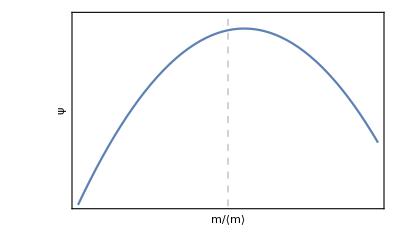

```mathematica
Plot[Log10@ψ[1,1][10^x],{x,-2,2},FrameLabel->{"m/⟨m⟩","ψ"},FrameTicks->{logticksx[1,1,1,1],logticksx[1,1,1,1]},GridLines->{{0},{}},GridLinesStyle->Directive[Gray, Dashed]]
```

```mathematica
AbsoluteTiming[clist = ParallelMap[{#,
Quiet@{constr[ψ[10^#,1],accf,0,5],
constr[ψ[10^#,1],OGLEf,-8,5],
constr[ψ[10^#,1],OGLEhcf,-8,5],
constr[ψ[10^#,1],EROSf,-8,5],
constr[ψ[10^#,1],SUBf,-11,-3],
constr[ψ[10^#,1],LIGOf,-2,5],
constr[ψ[10^#,1],BBNf,-25.,-14.],
constr[ψ[10^#,1],CMBf,-25.,-14.],
constr[ψ[10^#,1],EGRf,-25.,-14.],
constr[ψ[10^#,1],Voyagerf,-25.,-15.]}}&,
Table[mavg,{mavg,-24,4.4,0.2}]];][[1]]/60.
```

0.0675103

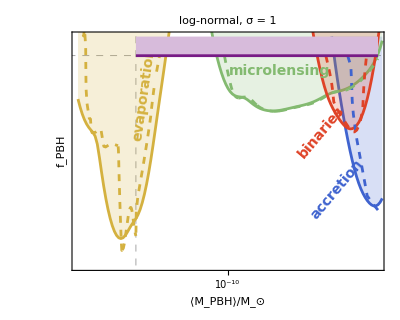

```mathematica
Show[ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,1]]]]}&/@clist,Joined->True,PlotRange->{{-24,4},{-11,1}},Filling->Top,PlotStyle->ColorData["Rainbow"][0.2],PlotRangePadding->None,ImagePadding->{{58,4},{42,10}},GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"⟨M_PBH⟩/"<>Msunt,"f_PBH"},FrameTicks->{logticksx[1,1,1,1],logticksx[5,5,10,1]},AspectRatio->0.8,ImageSize->400],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,2;;5]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.5],None}],
ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,6]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->ColorData["Rainbow"][0.95]],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,7;;10]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.72],None}],
Plot[accf[x],{x,0,4},PlotRange->{{-24,4},{-11,0}},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.2]]],
Plot[Log10[1/(1/10^SUBf[x]+1/10^EROSf[x]+1/10^OGLEf[x]+1/10^OGLEhcf[x])],{x,-11,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.5]]],
Plot[LIGOf[x],{x,-2,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.95]]],
Plot[Log10[1/(1/10^BBNf[x]+1/10^CMBf[x]+1/10^EGRf[x]+1/10^Voyagerf[x])],{x,-24,-15},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.72]]],
Plot[0,{x,Log10@Mevap,4},Filling->Top,PlotStyle->ColorData["Rainbow"][0.],FillingStyle->Opacity[1,Lighter[ColorData["Rainbow"][0.],0.7]]],Graphics[Text[Rotate[Style["evaporation",14,Bold,ColorData["Rainbow"][0.72]],82Degree],{-17.8,-2}]],
Graphics[Text[Rotate[Style["microlensing",14,Bold,ColorData["Rainbow"][0.5]],0Degree],{-5.2,-0.8}]],
Graphics[Text[Rotate[Style["binaries",14,Bold,ColorData["Rainbow"][0.95]],50Degree],{-1.3,-4}]],
Graphics[Text[Rotate[Style["accretion",14,Bold,ColorData["Rainbow"][0.2]],50Degree],{0.2,-7}]],
PlotLabel->Style["log-normal, σ = 1",16],ImagePadding->{{Automatic, 10}, {Automatic, 5}}]
```

```mathematica
AbsoluteTiming[clist = ParallelMap[{#[[1]],#[[2]],
Quiet@{constr[ψ[10^#[[1]],#[[2]]],accf,0,5],
constr[ψ[10^#[[1]],#[[2]]],OGLEf,-8,5],
constr[ψ[10^#[[1]],#[[2]]],OGLEhcf,-8,5],
constr[ψ[10^#[[1]],#[[2]]],EROSf,-8,5],
constr[ψ[10^#[[1]],#[[2]]],SUBf,-11,-3],
constr[ψ[10^#[[1]],#[[2]]],LIGOf,-2,5],
constr[ψ[10^#[[1]],#[[2]]],BBNf,-25.,-14.],
constr[ψ[10^#[[1]],#[[2]]],CMBf,-25.,-14.],
constr[ψ[10^#[[1]],#[[2]]],EGRf,-25.,-14.],
constr[ψ[10^#[[1]],#[[2]]],Voyagerf,-25.,-15.]}}&,
Flatten[Table[{mavg,σ},{mavg,-18.,3.,0.1},{σ,0.1,7.,0.1}],1]];][[1]]/60.
```

10.2116

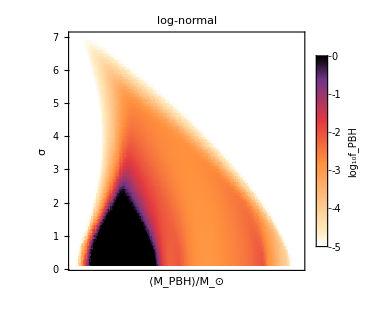

```mathematica
colorf = Blend[{{0,White},{0.08,RGBColor[1, 0.92, 0.75]},{0.44,RGBColor[1, 0.5700000000000001, 0.24]},{0.66,RGBColor[0.89, 0.22, 0.25]},{0.88,RGBColor[0.43, 0.21, 0.53]},{1,Black}},#1]&;
ListDensityPlot[{#[[1]],#[[2]],Log10[1/Max[1.01,Total[#[[3]]]]]}&/@clist,PlotRange->{All,All,{-5.,0.}},InterpolationOrder->1,ColorFunction->colorf,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{12, 120},LabelStyle->{Black,FontSize-> 12,FontFamily->"Times"},LegendLabel->Style["log_10f_PBH",14]],Scaled@{0.85,0.7}](*,MeshFunctions->{#3&},Mesh->4,MeshStyle->Directive[Dashed,White]*),FrameLabel->{"⟨M_PBH⟩/"<>Msunt,"σ"},FrameTicks->{Automatic,logticksx[5,5,10,1]},ImageSize->320,PlotLabel->Style["log-normal",16],ImagePadding->{{Automatic, 10}, {Automatic, 5}}]
```

### Critical collapse

```mathematica
(* fix the mass function so that it is normalized to unity and the mean mass is mavg *)
ψ[mavg_]=n(#/mavg)^(1+1/γ) Exp[-c(#/mavg)]&;
nsol = First@Solve[1==Integrate[ψ[mavg][m]/m,{m,0,Infinity},Assumptions->{mavg>0,c>0,n>0,γ>0}],n]
csol = First@Solve[mavg ==1/Integrate[ψ[mavg][m]/m^2,{m,0,Infinity},Assumptions->{mavg>0,c>0,n>0,γ>0}]/.nsol,c]
ψ[mavg_] = ψ[mavg]/.nsol/.csol/.γ->0.36;
ψ[mavg][m]
```

{n→c^(1+1/γ)/Gamma[1+1/γ]}

{c→Gamma[1+1/γ]/Gamma[1/γ]}

10.3791 ⅇ^(-(2.77778 m)/mavg) (m/mavg)^3.77778

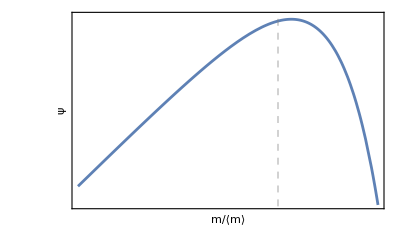

```mathematica
Plot[Log10@ψ[1][10^x],{x,-2,1},FrameLabel->{"m/⟨m⟩","ψ"},FrameTicks->{logticksx[1,1,1,1],logticksx[1,1,1,1]},GridLines->{{0},{}},GridLinesStyle->Directive[Gray, Dashed]]
```

```mathematica
AbsoluteTiming[clist = ParallelMap[{#,
Quiet@{constr[ψ[10^#],accf,0,5],
constr[ψ[10^#],OGLEf,-8,5],
constr[ψ[10^#],OGLEhcf,-8,5],
constr[ψ[10^#],EROSf,-8,5],
constr[ψ[10^#],SUBf,-11,-3],
constr[ψ[10^#],LIGOf,-2,5],
constr[ψ[10^#],BBNf,-25.,-14.],
constr[ψ[10^#],CMBf,-25.,-14.],
constr[ψ[10^#],EGRf,-25.,-14.],
constr[ψ[10^#],Voyagerf,-25.,-15.]}}&,
Table[mavg,{mavg,-24,4.4,0.2}]];][[1]]/60.
```

0.0706269

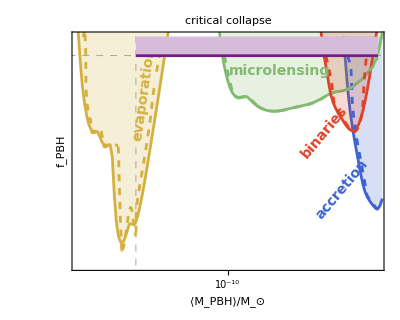

```mathematica
Show[ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,1]]]]}&/@clist,Joined->True,PlotRange->{{-24,4},{-11,1}},Filling->Top,PlotStyle->ColorData["Rainbow"][0.2],PlotRangePadding->None,ImagePadding->{{58,4},{42,10}},GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"⟨M_PBH⟩/"<>Msunt,"f_PBH"},FrameTicks->{logticksx[1,1,1,1],logticksx[5,5,10,1]},AspectRatio->0.8,ImageSize->400],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,2;;5]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.5],None}],
ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,6]]]]}&/@clist,Joined->True,PlotRange->All,Filling->Top,PlotStyle->ColorData["Rainbow"][0.95]],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,7;;10]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.72],None}],
Plot[accf[x],{x,0,4},PlotRange->{{-24,4},{-11,0}},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.2]]],
Plot[Log10[1/(1/10^SUBf[x]+1/10^EROSf[x]+1/10^OGLEf[x]+1/10^OGLEhcf[x])],{x,-11,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.5]]],
Plot[LIGOf[x],{x,-2,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.95]]],
Plot[Log10[1/(1/10^BBNf[x]+1/10^CMBf[x]+1/10^EGRf[x]+1/10^Voyagerf[x])],{x,-24,-15},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.72]]],
Plot[0,{x,Log10@Mevap,4},Filling->Top,PlotStyle->ColorData["Rainbow"][0.],FillingStyle->Opacity[1,Lighter[ColorData["Rainbow"][0.],0.7]]],Graphics[Text[Rotate[Style["evaporation",14,Bold,ColorData["Rainbow"][0.72]],82Degree],{-17.8,-2}]],
Graphics[Text[Rotate[Style["microlensing",14,Bold,ColorData["Rainbow"][0.5]],0Degree],{-5.2,-0.8}]],
Graphics[Text[Rotate[Style["binaries",14,Bold,ColorData["Rainbow"][0.95]],50Degree],{-1,-4}]],
Graphics[Text[Rotate[Style["accretion",14,Bold,ColorData["Rainbow"][0.2]],50Degree],{0.6,-7}]],
PlotLabel->Style["critical collapse",16],ImagePadding->{{Automatic, 10}, {Automatic, 5}}]
```

### Cut power-law

```mathematica
(* fix the mass function so that it is normalized to unity *)
ψ[mmin_,mmax_,α_]=n#^α UnitStep[#-mmin]UnitStep[mmax-#]&;
nsol = Last@Solve[1==Integrate[ψ[mmin,mmax,α][m]/m,{m,0,Infinity},Assumptions->{mmin>0,mmax>mmin,n>0}],n]
ψ[mmin_,mmax_,α_] = ψ[mmin,mmax,α]/.nsol;
ψ[mmin,mmax,α][m]
```

{n→α/(mmax^α-mmin^α)}

(m^α α UnitStep[-m+mmax] UnitStep[m-mmin])/(mmax^α-mmin^α)

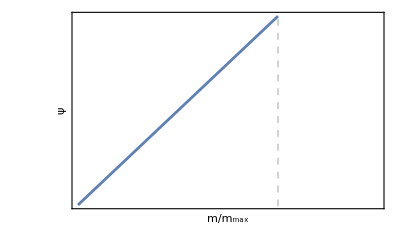

```mathematica
Plot[Log10@ψ[0,1,1][10^x],{x,-2,1},FrameLabel->{"m/m_max","ψ"},FrameTicks->{logticksx[1,1,1,1],logticksx[1,1,1,1]},GridLines->{{0},{}},GridLinesStyle->Directive[Gray, Dashed]]
```

```mathematica
α0 = 1;
AbsoluteTiming[clist = ParallelMap[{#,
Quiet@{constr[ψ[0,10^#,α0],accf,0,5],
constr[ψ[0,10^#,α0],OGLEf,-8,5],
constr[ψ[0,10^#,α0],OGLEhcf,-8,5],
constr[ψ[0,10^#,α0],EROSf,-8,5],
constr[ψ[0,10^#,α0],SUBf,-11,-3],
constr[ψ[0,10^#,α0],LIGOf,-2,5],
constr[ψ[0,10^#,α0],BBNf,-25.,-14.],
constr[ψ[0,10^#,α0],CMBf,-25.,-14.],
constr[ψ[0,10^#,α0],EGRf,-25.,-14.],
constr[ψ[0,10^#,α0],Voyagerf,-25.,-15.]}}&,
Table[mmax,{mmax,-24,4.4,0.2}]];][[1]]/60.
```

0.688145

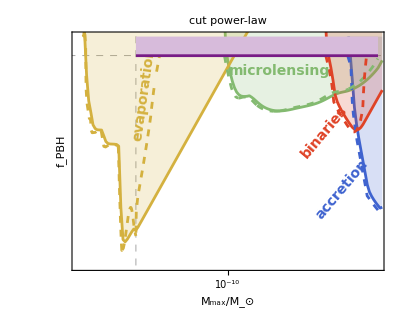

```mathematica
Show[ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,1]]]]}&/@clist,Joined->True,PlotRange->{{-24,4},{-11,1}},Filling->Top,PlotStyle->ColorData["Rainbow"][0.2],PlotRangePadding->None,ImagePadding->{{58,4},{42,10}},GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"M_max/"<>Msunt,"f_PBH"},FrameTicks->{logticksx[1,1,1,1],logticksx[5,5,10,1]},AspectRatio->0.8,ImageSize->400],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,2;;5]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.5],None}],
ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,6]]]]}&/@clist,Joined->True,PlotRange->All,Filling->Top,PlotStyle->ColorData["Rainbow"][0.95]],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,7;;10]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.72],None}],
Plot[accf[x],{x,0,4},PlotRange->{{-24,4},{-11,0}},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.2]]],
Plot[Log10[1/(1/10^SUBf[x]+1/10^EROSf[x]+1/10^OGLEf[x]+1/10^OGLEhcf[x])],{x,-11,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.5]]],
Plot[LIGOf[x],{x,-2,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.95]]],
Plot[Log10[1/(1/10^BBNf[x]+1/10^CMBf[x]+1/10^EGRf[x]+1/10^Voyagerf[x])],{x,-24,-15},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.72]]],
Plot[0,{x,Log10@Mevap,4},Filling->Top,PlotStyle->ColorData["Rainbow"][0.],FillingStyle->Opacity[1,Lighter[ColorData["Rainbow"][0.],0.7]]],Graphics[Text[Rotate[Style["evaporation",14,Bold,ColorData["Rainbow"][0.72]],82Degree],{-17.8,-2}]],
Graphics[Text[Rotate[Style["microlensing",14,Bold,ColorData["Rainbow"][0.5]],0Degree],{-5.2,-0.8}]],
Graphics[Text[Rotate[Style["binaries",14,Bold,ColorData["Rainbow"][0.95]],50Degree],{-1,-4}]],
Graphics[Text[Rotate[Style["accretion",14,Bold,ColorData["Rainbow"][0.2]],50Degree],{0.6,-7}]],
PlotLabel->Style["cut power-law",16],ImagePadding->{{Automatic, 10}, {Automatic, 5}}]
```

```mathematica
α0 = -1;
AbsoluteTiming[clist = ParallelMap[{#,
Quiet@{constr[ψ[10^#,10^20,α0],accf,0,5],
constr[ψ[10^#,10^20,α0],OGLEf,-8,5],
constr[ψ[10^#,10^20,α0],OGLEhcf,-8,5],
constr[ψ[10^#,10^20,α0],EROSf,-8,5],
constr[ψ[10^#,10^20,α0],SUBf,-11,-3],
constr[ψ[10^#,10^20,α0],LIGOf,-2,5],
constr[ψ[10^#,10^20,α0],BBNf,-25.,-14.],
constr[ψ[10^#,10^20,α0],CMBf,-25.,-14.],
constr[ψ[10^#,10^20,α0],EGRf,-25.,-14.],
constr[ψ[10^#,10^20,α0],Voyagerf,-25.,-15.]}}&,
Table[mmax,{mmax,-24,4.4,0.2}]];][[1]]/60.
```

0.96449

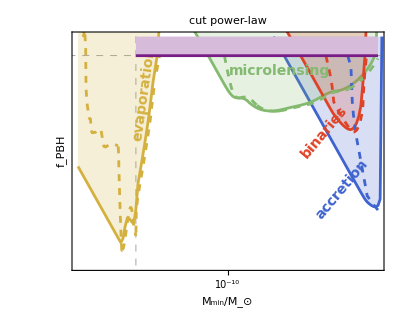

```mathematica
Show[ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,1]]]]}&/@clist,Joined->True,PlotRange->{{-24,4},{-11,1}},Filling->Top,PlotStyle->ColorData["Rainbow"][0.2],PlotRangePadding->None,ImagePadding->{{58,4},{42,10}},GridLines->{{Log10@Mevap},{0}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"M_min/"<>Msunt,"f_PBH"},FrameTicks->{logticksx[1,1,1,1],logticksx[5,5,10,1]},AspectRatio->0.8,ImageSize->400],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,2;;5]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.5],None}],
ListPlot[{#[[1]],Log10[1/Max[0.001,#[[2,6]]]]}&/@clist,Joined->True,PlotRange->All,Filling->Top,PlotStyle->ColorData["Rainbow"][0.95]],
ListPlot[{#[[1]],Log10[1/Max[0.001,Total[#[[2,7;;10]]]]]}&/@clist,PlotRange->All,Joined->True,Filling->Top,PlotStyle->{ColorData["Rainbow"][0.72],None}],
Plot[accf[x],{x,0,4},PlotRange->{{-24,4},{-11,0}},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.2]]],
Plot[Log10[1/(1/10^SUBf[x]+1/10^EROSf[x]+1/10^OGLEf[x]+1/10^OGLEhcf[x])],{x,-11,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.5]]],
Plot[LIGOf[x],{x,-2,4},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.95]]],
Plot[Log10[1/(1/10^BBNf[x]+1/10^CMBf[x]+1/10^EGRf[x]+1/10^Voyagerf[x])],{x,-24,-15},PlotStyle->Directive[Dashed,ColorData["Rainbow"][0.72]]],
Plot[0,{x,Log10@Mevap,4},Filling->Top,PlotStyle->ColorData["Rainbow"][0.],FillingStyle->Opacity[1,Lighter[ColorData["Rainbow"][0.],0.7]]],Graphics[Text[Rotate[Style["evaporation",14,Bold,ColorData["Rainbow"][0.72]],82Degree],{-17.8,-2}]],
Graphics[Text[Rotate[Style["microlensing",14,Bold,ColorData["Rainbow"][0.5]],0Degree],{-5.2,-0.8}]],
Graphics[Text[Rotate[Style["binaries",14,Bold,ColorData["Rainbow"][0.95]],50Degree],{-1,-4}]],
Graphics[Text[Rotate[Style["accretion",14,Bold,ColorData["Rainbow"][0.2]],50Degree],{0.6,-7}]],
PlotLabel->Style["cut power-law",16],ImagePadding->{{Automatic, 10}, {Automatic, 5}}]
```

```mathematica
AbsoluteTiming[clist = ParallelMap[{#[[1]],-10^#[[2]],
Quiet@{constr[ψ[10^#[[1]],10^20,-10^#[[2]]],accf,0,5],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],OGLEf,-8,5],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],OGLEhcf,-8,5],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],EROSf,-8,5],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],SUBf,-11,-3],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],LIGOf,-2,5],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],BBNf,-25.,-14.],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],CMBf,-25.,-14.],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],EGRf,-25.,-14.],
constr[ψ[10^#[[1]],10^20,-10^#[[2]]],Voyagerf,-25.,-15.]}}&,
Flatten[Table[{mmin,logα},{mmin,-18.,3.,0.2},{logα,Subdivide[-1.,Log10@2.,30]}],1]];][[1]]/60.
```

26.065

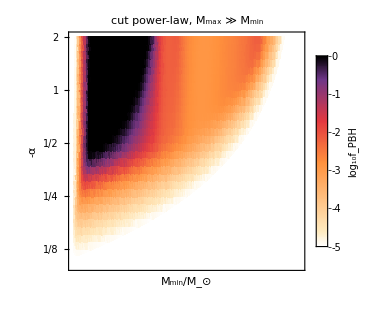

```mathematica
colorf = Blend[{{0,White},{0.08,RGBColor[1, 0.92, 0.75]},{0.44,RGBColor[1, 0.5700000000000001, 0.24]},{0.66,RGBColor[0.89, 0.22, 0.25]},{0.88,RGBColor[0.43, 0.21, 0.53]},{1,Black}},#1]&;
ListDensityPlot[{#[[1]],Log10[-#[[2]]],Log10[1/Max[1.01,Total[#[[3]]]]]}&/@clist,PlotRange->{All,All,{-5.,0.}},InterpolationOrder->1,ColorFunction->colorf,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{12, 120},LabelStyle->{Black,FontSize-> 12,FontFamily->"Times"},LegendLabel->Style["log_10f_PBH",14]],Scaled@{0.85,0.3}](*,MeshFunctions->{#3&},Mesh->4,MeshStyle->Directive[Dashed,White]*),FrameLabel->{"M_min/"<>Msunt,"-α"},FrameTicks->{{{{Log10[1/8],"1/"<>ToString@8},{Log10[1/6],"1/"<>ToString@6},{Log10[1/4],"1/"<>ToString@4},{Log10[1/3],"1/"<>ToString@3},{Log10[1/2],"1/"<>ToString@2},{Log10[2/3],ToString[2]<>"/"<>ToString[3]},{Log10@1,1},{Log10[3/2],ToString[3]<>"/"<>ToString[2]},{Log10@2,2}},{{Log10[1/8],""},{Log10[1/6],""},{Log10[1/4],""},{Log10[1/3],""},{Log10[1/2],""},{Log10[2/3],""},{Log10@1,""},{Log10[3/2],""},{Log10@2,""}}},logticksx[5,5,10,1]},ImageSize->320,PlotLabel->Style["cut power-law, M_max ≫ M_min",16],ImagePadding->{{Automatic, 10}, {Automatic, 5}}]
```

```mathematica
AbsoluteTiming[clist2 = ParallelMap[{#[[1]],10^#[[2]],
Quiet@{constr[ψ[10^-25,10^#[[1]],10^#[[2]]],accf,0,5],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],OGLEf,-8,5],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],OGLEhcf,-8,5],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],EROSf,-8,5],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],SUBf,-11,-3],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],LIGOf,-2,5],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],BBNf,-25.,-14.],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],CMBf,-25.,-14.],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],EGRf,-25.,-14.],
constr[ψ[10^-25,10^#[[1]],10^#[[2]]],Voyagerf,-25.,-15.]}}&,
Flatten[Table[{mmax,logα},{mmax,-18.,3.,0.2},{logα,Subdivide[-1.,Log10@2.,30]}],1]];][[1]]/60.
```

28.9955

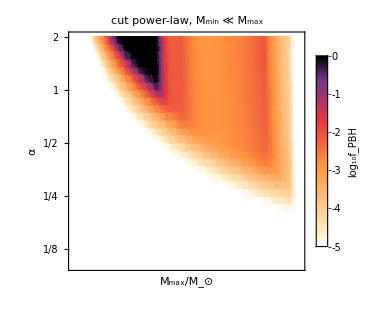

```mathematica
colorf = Blend[{{0,White},{0.08,RGBColor[1, 0.92, 0.75]},{0.44,RGBColor[1, 0.5700000000000001, 0.24]},{0.66,RGBColor[0.89, 0.22, 0.25]},{0.88,RGBColor[0.43, 0.21, 0.53]},{1,Black}},#1]&;
ListDensityPlot[{#[[1]],Log10[#[[2]]],Log10[1/Max[1.01,Total[#[[3]]]]]}&/@clist2,PlotRange->{All,All,{-5.,0.}},InterpolationOrder->1,ColorFunction->colorf,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->{12, 120},LabelStyle->{Black,FontSize-> 12,FontFamily->"Times"},LegendLabel->Style["log_10f_PBH",14]],Scaled@{0.16,0.3}](*,MeshFunctions->{#3&},Mesh->4,MeshStyle->Directive[Dashed,White]*),FrameLabel->{"M_max/"<>Msunt,"α"},FrameTicks->{{{{Log10[1/8],"1/"<>ToString@8},{Log10[1/6],"1/"<>ToString@6},{Log10[1/4],"1/"<>ToString@4},{Log10[1/3],"1/"<>ToString@3},{Log10[1/2],"1/"<>ToString@2},{Log10[2/3],ToString[2]<>"/"<>ToString[3]},{Log10@1,1},{Log10[3/2],ToString[3]<>"/"<>ToString[2]},{Log10@2,2}},{{Log10[1/8],""},{Log10[1/6],""},{Log10[1/4],""},{Log10[1/3],""},{Log10[1/2],""},{Log10[2/3],""},{Log10@1,""},{Log10[3/2],""},{Log10@2,""}}},logticksx[5,5,10,1]},ImageSize->320,PlotLabel->Style["cut power-law, M_min ≪ M_max",16],ImagePadding->{{Automatic, 10}, {Automatic, 5}}]
```